# Cosmology: Problem 2

```mathematica
params = {Subscript[H, 0]->0.7*^-10,Subscript[Ω, V]->(1-Subscript[Ω, M])};
ageUniverse = 13.8*^9;
```

```mathematica
ClearAll [MPLColorMap];
<<"http://pastebin.com/raw/pFsb4ZBS";
viridis = MPLColorMap ["Viridis"][0.6];
viridis1 = MPLColorMap ["Viridis"][0.9];
```

```mathematica
t0 = 1/Subscript[H, 0] Integrate[1/(a Sqrt[Subscript[Ω, M]/a^3+Subscript[Ω, V]]),{a,0,1},Assumptions->{Subscript[Ω, M]>0,Subscript[Ω, V]>0}]
```

(2 ArcSinh[√(Ω_V/Ω_M)])/(3 H_0 √Ω_V)

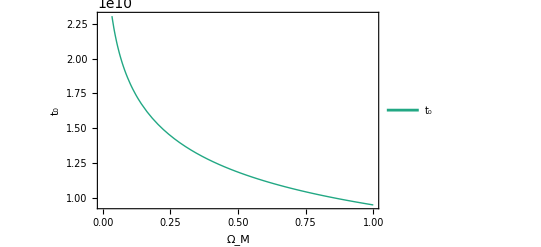

```mathematica
(*Normal Plot*)
fig1 = Plot[t0/.params,{Subscript[Ω, M],0,1}, Frame->True, PlotStyle->{viridis, Thick}, FrameLabel->{"Ω_M", "t_0"},PlotLegends->{"t_0"}]
```

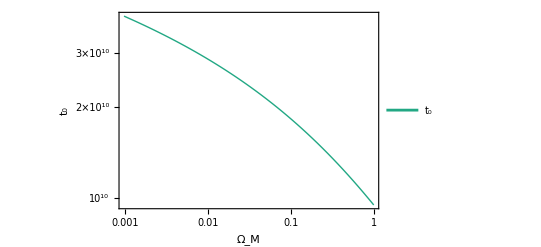

```mathematica
(*Log-Log Plot*)
fig2 = Plot[t0/.params,{Subscript[Ω, M],0,1}, 
ScalingFunctions->{"Log","Log"}, 
Frame->True, 
PlotStyle->{viridis, Thick},
 FrameLabel->{"Ω_M", "t_0"},
PlotLegends->{"t_0"}]
```

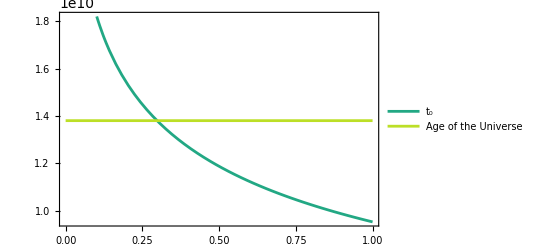

```mathematica
(*Evolution of Subscript[t, 0] and the age of the universe*)
fig3 = Plot[{t0/.params,ageUniverse},{Subscript[Ω, M],0,1}, PlotStyle->{viridis,viridis1}, Frame->True, PlotLegends->{"t_0","Age of the Universe"}]
```

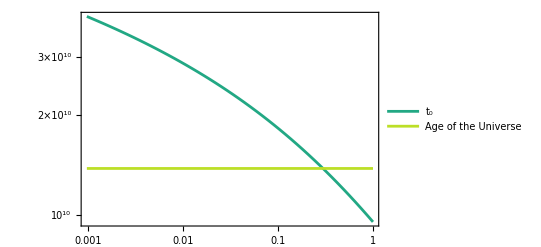

```mathematica
fig4 = Plot[{t0/.params,ageUniverse},{Subscript[Ω, M],0,1}, 
PlotStyle->{viridis,viridis1}, 
Frame->True, 
ScalingFunctions->{"Log", "Log"},
PlotLegends->{"t_0","Age of the Universe"}]
```

```mathematica
sol = NSolve[(t0/.params/.Subscript[Ω, M]->x)-ageUniverse==0,x][[1]]
```

{x→0.297893}